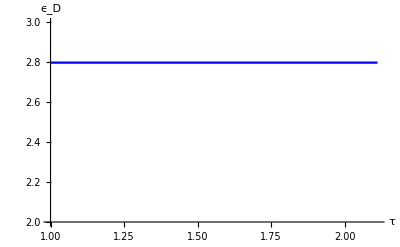

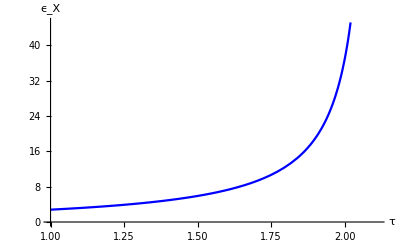

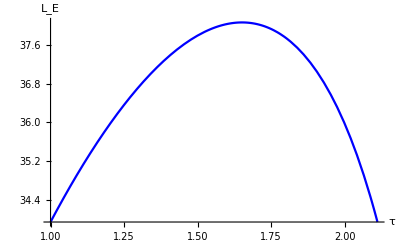

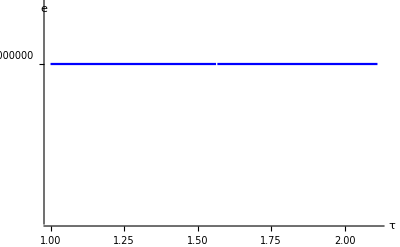

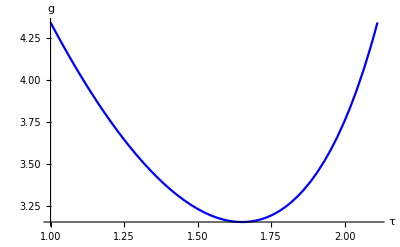

-Graphics-

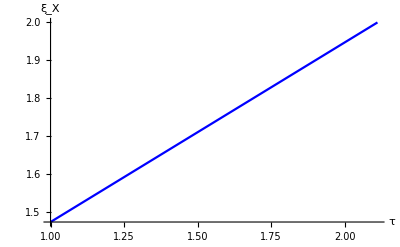

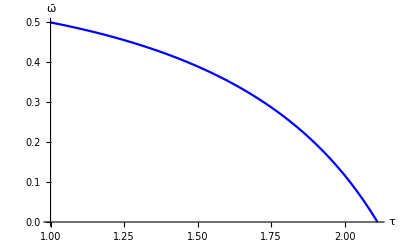

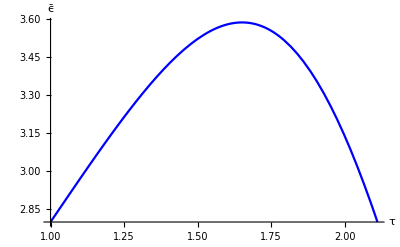

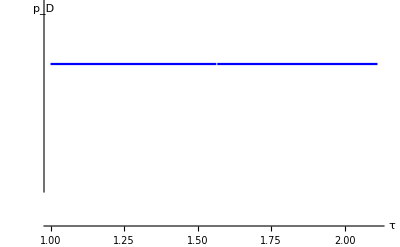

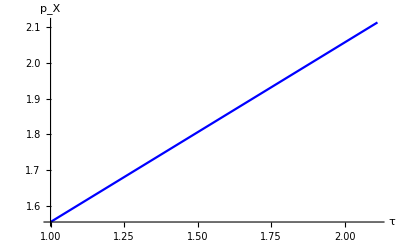

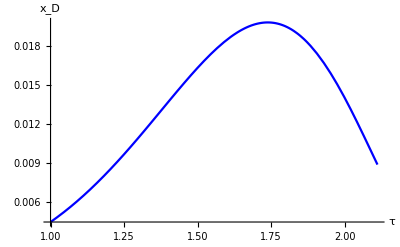

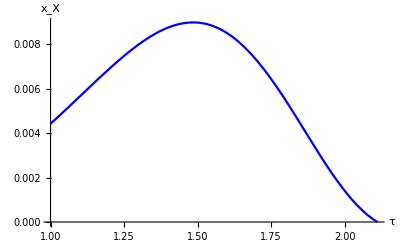

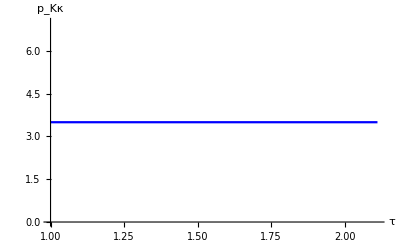

```mathematica
(*This file simulates how the addilog model with Grossman-Helpman specification of p_K responds to the change of trade costs.*)
v[x_]=1/(1+γ) (b-x)^(1+γ); 
ϵ[x_]=-(x v''[x])/v'[x];
Subscript[ϵ, D]=ϵ[Subscript[ξ, D]];
Subscript[ϵ, X]=ϵ[Subscript[ξ, X]];
parameters={κ-> 7 ,ρ->0.8,w->1,L->50,δ->0.25,ψ->1,b->2,γ->1};
eqn1=Subscript[ξ, D] (1-1/Subscript[ϵ, D])τ-Subscript[ξ, X](1-1/Subscript[ϵ, X])==0;
eqn2=1/(ε̃)-(1-ω̃)1/Subscript[ϵ, D]-ω̃ 1/Subscript[ϵ, X]==0;
eqn3=g+δ-(w L (1+ψ))/κ(1-(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]]))==0;
eqn4=g-(w L (1+ψ))/(κ ε̃)+(ρ(ε̃-1))/(ε̃)+δ==0;
eqn5= ω̃-(Subscript[ξ, X] v'[Subscript[ξ, X]])/(Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])==0;
eqn6= e Subscript[ξ, X](1-1/Subscript[ϵ, X])-τ w==0;
eqn7 =Le (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]])-L(v'[Subscript[ξ, D]]+τ v'[Subscript[ξ, X]])==0;

neweqn1L=eqn1/.parameters;
neweqn2L=eqn2/.parameters;
neweqn3L=eqn3/.parameters;
neweqn4L=eqn4/.parameters;
neweqn5L=eqn5/.parameters;
neweqn6L=eqn6/.parameters;
neweqn7L=eqn7/.parameters;
Nvalue=Exp[g] /.parameters;(*we normalize N0=1, and consider t=1 *)
muvalue=Exp[g] (Subscript[ξ, D] v'[Subscript[ξ, D]]+Subscript[ξ, X] v'[Subscript[ξ, X]] );(*we normalize N0=1, and consider t=1 *)
AutEq=v'[Subscript[ξ, X]]==0/.parameters;AutTau=τ/.FindRoot[{AutEq,neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{τ,2.3},{Subscript[ξ, D],0.5},{Subscript[ξ, X],2},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}];

additauGH1=Plot[Subscript[ϵ, D]/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,AutTau},PlotRange->{{1,AutTau},{2,3}},PlotStyle->Blue,AxesLabel-> {τ,"ϵ_D" }]
additauGH2=Plot[Subscript[ϵ, X]/.parameters/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"ϵ_X" }]
additauGH3=Plot[Le/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"L_E" }]

additauGH4=Plot[e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"e" }]
additauGH5=Plot[g/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"g" }]
additauGH6=Plot[Subscript[ξ, D]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"ξ_D" }]
additauGH7=Plot[Subscript[ξ, X]/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"ξ_X" }]
additauGH8=Plot[ω̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"ω̄" }]
additauGH9=Plot[ε̃/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"ϵ̄" }]
additauGH10=Plot[Subscript[ξ, D] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"p_D" }]
additauGH11=Plot[Subscript[ξ, X] e/.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"p_X" }]
additauGH12=Plot[v'[Subscript[ξ, D]]/muvalue/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"x_D"}]
additauGH13=Plot[v'[Subscript[ξ, X]]/muvalue/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,"x_X"} ]
additauGH14=Plot[κ/(1+ψ)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,AutTau},PlotStyle-> Blue,PlotStyle->Blue,AxesLabel-> {τ,"p_Kκ"}]
additauGH15=Plot[1/ρ(Log[v[Subscript[ξ, D]]+v[Subscript[ξ, X]]]+ g/ρ)/.parameters /.FindRoot[{neweqn1L,neweqn2L,neweqn3L,neweqn4L,neweqn5L,neweqn6L,neweqn7L},{{Subscript[ξ, D],0.5},{Subscript[ξ, X],0.6},{ε̃,1.5},{ω̃,0.6},{g,0.8},{e,1},{Le,20}}],{τ,1,AutTau},PlotStyle->Blue,AxesLabel-> {τ,Welfare} ]
```

```mathematica
alladditauGH={{additauGH1,additauGH2,additauGH3,additauGH4},{additauGH5,additauGH6,additauGH7,additauGH8},{additauGH9,additauGH10,additauGH11,additauGH12},{additauGH13,additauGH14,additauGH15}}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}